```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=ReadList["!./hw 1000 1e-10 | awk '/^phi/{print $2, $3, $4}'",{Number,Number,Number}];
```

```mathematica
ListContourPlot[data,Contours->{5,25,50,75,95},ContourLabels->All,Epilog->Disk[{0,0},10]]
```

-Graphics-

```mathematica
datae=ReadList["!./hw 5 1e-1 | awk '/^efield/{print $2, $3, $4, $5}'",{Number,Number,Number,Number}];
```

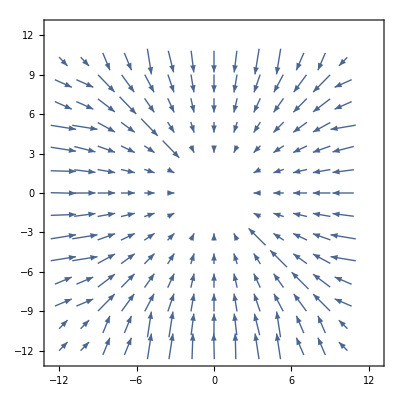

```mathematica
ListVectorPlot[datae,RegionFunction->Function[{x,y},Abs[x]>0.5||Abs[y]>0.5],VectorScale->0.06]
```